```mathematica
LEFT=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[ω]<>".dat"]],{ω,Range[0,3,0.01]}]
```

{1}
 |  |  |  |

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[[ω*100+1]].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[[ω*100+1]].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

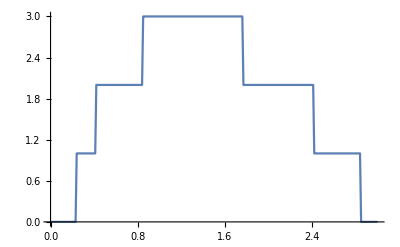

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]]
```

```mathematica
greenfunctions[ω_,δ_,t_,ϵ_,ϵ1_,START_,STOP_]:=Module[{J=SL[ω,δ,t,ϵ],b,il,gnk},
imp:=Inverse[β[ω,δ,t,ϵ]];
list={{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp}};
b[n_]:=
Module[{},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].T1[t].J.T1[t]].list[[1,ζ]],{ζ,1,n}];
 J=J];
ir:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].b[STOP].TT[t]].SL[ω,δ,t,ϵ];
gnk[κ_,ι_,Τ_]:=Module[{},
gik=Module[{φ=b[κ].ConjugateTranspose[T1[t]].b[κ+1]},Do[φ=φ.ConjugateTranspose[T1[t]].b[l],{l,κ+2,ι}];
φ=φ];
gik].ConjugateTranspose[T1[t]].ir;
gnk[START,STOP,t]]
```

```mathematica
greenfunctions[0,0.0001,1,0,0,1,99]
```

{{0.-6.98028×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,-4.08895×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.-6.98028×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.-5.78265×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,-2.89133×10^29+0. ⅈ},{-9.87161×10^21+0. ⅈ,0.-4.08895×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.+5.78265×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.-4.08895×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ,5.78265×10^21+0. ⅈ,0.-1.6937×10^25 ⅈ,-8.17791×10^21+0. ⅈ,0.-1.6937×10^25 ⅈ,5.78265×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ},{0.+2.89133×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.-1.19763×10^25 ⅈ,1.6937×10^29+0. ⅈ,0.-1.19763×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.-1.6937×10^25 ⅈ,-4.96073×10^28+0. ⅈ,0.+2.39525×10^25 ⅈ,-4.96073×10^28+0. ⅈ,0.-1.6937×10^25 ⅈ,1.19763×10^29+0. ⅈ},{1.39606×10^22+0. ⅈ,0.+5.78265×10^25 ⅈ,-5.78265×10^21+0. ⅈ,0.-8.17791×10^25 ⅈ,-5.78265×10^21+0. ⅈ,0.+5.78265×10^25 ⅈ,1.39606×10^22+0. ⅈ,0.-5.78265×10^25 ⅈ,-8.17791×10^21+0. ⅈ,0.+2.39525×10^25 ⅈ,1.15653×10^22+0. ⅈ,0.+2.39525×10^25 ⅈ,-8.17791×10^21+0. ⅈ,0.-5.78265×10^25 ⅈ},{0.+2.89133×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.-1.19763×10^25 ⅈ,1.6937×10^29+0. ⅈ,0.-1.19763×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.-1.6937×10^25 ⅈ,-4.96073×10^28+0. ⅈ,0.+2.39525×10^25 ⅈ,-4.96073×10^28+0. ⅈ,0.-1.6937×10^25 ⅈ,1.19763×10^29+0. ⅈ},{-9.87161×10^21+0. ⅈ,0.-4.08895×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.+5.78265×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.-4.08895×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ,5.78265×10^21+0. ⅈ,0.-1.6937×10^25 ⅈ,-8.17791×10^21+0. ⅈ,0.-1.6937×10^25 ⅈ,5.78265×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ},{0.-6.98028×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,-4.08895×10^29+0. ⅈ,0.+2.89133×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.-6.98028×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.-5.78265×10^25 ⅈ,1.19763×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,-2.89133×10^29+0. ⅈ},{1.68519×10^22+0. ⅈ,0.+6.98028×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.-9.87161×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.+6.98028×10^25 ⅈ,1.68519×10^22+0. ⅈ,0.-6.98028×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ,1.39606×10^22+0. ⅈ,0.+2.89133×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.-6.98028×10^25 ⅈ},{0.+6.98028×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.-2.89133×10^25 ⅈ,4.08895×10^29+0. ⅈ,0.-2.89133×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.+6.98028×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.-4.08895×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.+5.78265×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.-4.08895×10^25 ⅈ,2.89133×10^29+0. ⅈ},{-6.98028×10^21+0. ⅈ,0.-2.89133×10^25 ⅈ,2.89133×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ,2.89133×10^21+0. ⅈ,0.-2.89133×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.-1.19763×10^25 ⅈ,-5.78265×10^21+0. ⅈ,0.-1.19763×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ},{0.-9.87161×10^25 ⅈ,4.08895×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,-5.78265×10^29+0. ⅈ,0.+4.08895×10^25 ⅈ,4.08895×10^29+0. ⅈ,0.-9.87161×10^25 ⅈ,-4.08895×10^29+0. ⅈ,0.+5.78265×10^25 ⅈ,1.6937×10^29+0. ⅈ,0.-8.17791×10^25 ⅈ,1.6937×10^29+0. ⅈ,0.+5.78265×10^25 ⅈ,-4.08895×10^29+0. ⅈ},{-6.98028×10^21+0. ⅈ,0.-2.89133×10^25 ⅈ,2.89133×10^21+0. ⅈ,0.+4.08895×10^25 ⅈ,2.89133×10^21+0. ⅈ,0.-2.89133×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.-1.19763×10^25 ⅈ,-5.78265×10^21+0. ⅈ,0.-1.19763×10^25 ⅈ,4.08895×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ},{0.+6.98028×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.-2.89133×10^25 ⅈ,4.08895×10^29+0. ⅈ,0.-2.89133×10^25 ⅈ,-2.89133×10^29+0. ⅈ,0.+6.98028×10^25 ⅈ,2.89133×10^29+0. ⅈ,0.-4.08895×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.+5.78265×10^25 ⅈ,-1.19763×10^29+0. ⅈ,0.-4.08895×10^25 ⅈ,2.89133×10^29+0. ⅈ},{1.68519×10^22+0. ⅈ,0.+6.98028×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.-9.87161×10^25 ⅈ,-6.98028×10^21+0. ⅈ,0.+6.98028×10^25 ⅈ,1.68519×10^22+0. ⅈ,0.-6.98028×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.+2.89133×10^25 ⅈ,1.39606×10^22+0. ⅈ,0.+2.89133×10^25 ⅈ,-9.87161×10^21+0. ⅈ,0.-6.98028×10^25 ⅈ}}

```mathematica
Clear[Εl,Εr]
```

```mathematica
Εl[ω_]:=Εl[ω]=TT[1].SL[ω,0.0001,1,0].ConjugateTranspose[TT[1]]
```

```mathematica
Γl[ω_]:= ⅈ(Εl[ω]-ConjugateTranspose[Εl[ω]])
```

```mathematica
Εr[ω_]:=Εl[ω]=TT[1].SL[ω,0.0001,1,0].ConjugateTranspose[TT[1]]
```

```mathematica
Γr[ω_]:= ⅈ(Εr[ω]-ConjugateTranspose[Εr[ω]])
```

```mathematica
TRA2[ω_,ϵ1_]:=Abs[Tr[Γl[ω].greenfunctions[ω,0.0001,1,0,0,1,100].Γl[ω].ConjugateTranspose[greenfunctions[ω,0.0001,1,0,0,1,100]]]]
```

```mathematica
TRA2[0,0]
```

9.0251×10^38

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,0]},{ω,Range[0,3,0.01]}]]
```

Inverse::matsq: Argument {{{{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.968508+0. ⅈ,1.+0. ⅈ,1.0162+0. ⅈ,1.+0. ⅈ,0.968508+0. ⅈ,1.+0. ⅈ},«13»},«12»,{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.031492+0. ⅈ,0.+0. ⅈ,0.016195+0. ⅈ,0.+0. ⅈ,-0.031492+0. ⅈ,0.+0. ⅈ},«12»,{«1»}}},«13»} at position 1 is not a non-empty square matrix.

```mathematica
gnk[κ_,ι_,Τ_]:=Module[{},
gik=Module[{φ=b[κ].T[t].b[κ+1]},Do[φ=φ.T[t].b[l],{l,κ+2,ι}];
φ=φ]]
```

```mathematica
gnk[1,100,0]
```

b[1].T[t].b[2].T[t].b[3].T[t].b[4].T[t].b[5].T[t].b[6].T[t].b[7].T[t].b[8].T[t].b[9].T[t].b[10].T[t].b[11].T[t].b[12].T[t].b[13].T[t].b[14].T[t].b[15].T[t].b[16].T[t].b[17].T[t].b[18].T[t].b[19].T[t].b[20].T[t].b[21].T[t].b[22].T[t].b[23].T[t].b[24].T[t].b[25].T[t].b[26].T[t].b[27].T[t].b[28].T[t].b[29].T[t].b[30].T[t].b[31].T[t].b[32].T[t].b[33].T[t].b[34].T[t].b[35].T[t].b[36].T[t].b[37].T[t].b[38].T[t].b[39].T[t].b[40].T[t].b[41].T[t].b[42].T[t].b[43].T[t].b[44].T[t].b[45].T[t].b[46].T[t].b[47].T[t].b[48].T[t].b[49].T[t].b[50].T[t].b[51].T[t].b[52].T[t].b[53].T[t].b[54].T[t].b[55].T[t].b[56].T[t].b[57].T[t].b[58].T[t].b[59].T[t].b[60].T[t].b[61].T[t].b[62].T[t].b[63].T[t].b[64].T[t].b[65].T[t].b[66].T[t].b[67].T[t].b[68].T[t].b[69].T[t].b[70].T[t].b[71].T[t].b[72].T[t].b[73].T[t].b[74].T[t].b[75].T[t].b[76].T[t].b[77].T[t].b[78].T[t].b[79].T[t].b[80].T[t].b[81].T[t].b[82].T[t].b[83].T[t].b[84].T[t].b[85].T[t].b[86].T[t].b[87].T[t].b[88].T[t].b[89].T[t].b[90].T[t].b[91].T[t].b[92].T[t].b[93].T[t].b[94].T[t].b[95].T[t].b[96].T[t].b[97].T[t].b[98].T[t].b[99].T[t].b[100]